Importing Dataset

```mathematica
dataset = Import["http://www-groups.dcs.st-and.ac.uk/history/Indexes/Full_Chron.html",{"Hyperlinks"}];
```

```mathematica
dataset1 =Flatten[StringCases[dataset,"http://www-groups.dcs.st-and.ac.uk/history/Biographies/"~~__]];
```

```mathematica
dataset2 = Import[#,"Text"]&/@dataset1
```

{6706,8997,7335,26071,13189,8342,33967,14134,17034,14494,2755,22932,25623,32677,25710,28993,20588,22485,15680,26426,25808}
 |  |  |  |

## HTML Parser

```mathematica
TemplateApply;

$mapping=Reverse[Normal[Templating`HTML`PackagePrivate`$SafeHTMLEntities],{2}];

htmlToText[txt_String]:=StringReplace[txt,$mapping]
```

```mathematica
htmls= Map[htmlToText,dataset2]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,2755,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}
 |  |  |  |

## Exporting List of HTMLs

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jofre/Documents/GitHub/KateSummer2018S/StudentDeliverables

```mathematica
Export["htmlbiographies.mx",htmls,"MX"]
```

htmlbiographies.mx

```mathematica
Export["listURLs.mx",dataset1,"MX"]
```

listURLs.mx

```mathematica
htmlList = Import["htmlbiographies.mx"]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,13304,28030,15557,14923,2747,18501,21861,14801,22484,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}
 |  |  |  |

```mathematica
Export["Biography1.m",dataset2]
```

```mathematica
bios =Import["htmlbiographies.mx"]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,13304,28030,2751,14801,22484,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}
 |  |  |  |

```mathematica
ClearAll[x]
```

```mathematica
fullNames =StringCases[htmlList,"<h1>"~~x__~~"</h1>"->x];
```

```mathematica
birthdate= StringCases[htmlList, "Born:<font color=\"green\"> "~~Shortest[y__]~~"<br>"->y];
```

```mathematica
deathdate=StringCases[htmlList, "<font color=\"purple\">"~~Shortest[z__]~~"</font>"->z];
```

```mathematica
ClearAll[a]
```

```mathematica
StringCases[htmlList[[22]],"../Mathematicians/"~~Shortest[a__]~~".html"->a]
```

{Plato,Plato,Plato,Plato,Theodorus,Theodorus,Plato,Plato,Plato,Plato,Theodorus,Theodorus,Plato,Plato,Plato,Plato,Euclid,Euclid,Pappus,Pappus,Euclid,Euclid,Euclid,Euclid,Pythagoras,Pythagoras,Pappus,Pappus,Theodorus,Theodorus,Heath,Heath,Pappus,Pappus,Eudemus,Eudemus,Van_der_Waerden,Van_der_Waerden,Van_der_Waerden,Van_der_Waerden,Euclid,Euclid,Euclid,Euclid,Plato,Plato,Theodorus,Theodorus,Theodorus,Theodorus,Eudoxus,Eudoxus,Euclid,Euclid,Geminus,Geminus,Plato,Plato,Pappus,Pappus}

## Get Rid of JS stuff

```mathematica
Counts[Flatten[(StringCases[htmlList,"../Mathematicians/"~~Shortest[a__]~~".html"->a](StringContainsQ[#," "]&)->Nothing)]]
```

Counts::invl: The argument … is not a list.

Counts[{{},{1},2771,{1},{McMullen (StringContainsQ[#1, ]&),McMullen (StringContainsQ[#1, ]&),McMullen (StringContainsQ[#1, ]&),17,Fields (StringContainsQ[#1, ]&),Fields (StringContainsQ[#1, ]&)}}→7]
 |  |  |  |

```mathematica
"De_Morgan',550,800); return false;\">George Boole</m></font>\n</article><hr>\n<b><a href = \"../References/Walsh"
```

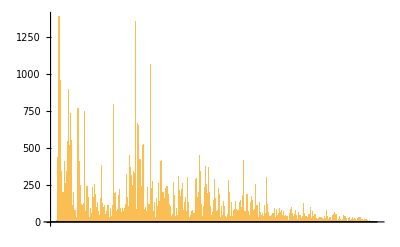

```mathematica
BarChart[Counts[Flatten[StringCases[htmlList,"../Mathematicians/"~~Shortest[a__]~~".html"->a]]]]
```

## Counting String Length

```mathematica
ClearAll[x];

getBodyBio [ htmlString_String ] := StringCases[ htmlString ,
                                                "<article>" ~~ Shortest[ x__ ] ~~ "</article>" -> x
                                                ];
                                                
deleteHtmlElements [ htmlString_String ] := StringDelete[
                                                          getBodyBio[ htmlString ],
                                                         "<"~~Shortest[__]~~">" 
                                                         ];
                                                         
numberSentences [ htmlString_String ] := Length@First@TextCases[ deleteHtmlElements [ htmlString ] , "Sentence"];

numberWords [ htmlString_String ] := Length@First@TextCases[ deleteHtmlElements [ htmlString ] , "Word"];
```

```mathematica
numberSentences[htmlList[[2]]]
```

22

```mathematica
numberWords[htmlList[[2]]]
```

477

```mathematica
StringCases[htmlList[[2]],"<article>"~~Shortest[x__]~~"</article>"->x];
```

{To write a biography of <b>Baudhayana</b> is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras. We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.
<p>
He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like <a href="../Mathematicians/Ahmes.html" onclick="javascript:win1('../Mathematicians/Ahmes.html',400,400); return false;">Ahmes</a>. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. 
<p>
The mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices. It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman. He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. 
<p>
The Sulbasutras are discussed in detail in the article <a href="../HistTopics/Indian_sulbasutras.html">Indian Sulbasutras</a>. Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.
<p>
The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown. Quadratic equations of the forms <i>ax</i><sup>2</sup> = <i>c</i> and <i>ax</i><sup>2</sup> + <i>bx</i> = <i>c</i> appear.
<p>
Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes. Constructions are given which are equivalent to taking &#960; equal to <sup>676</sup>/<sub>225</sub> (where <sup>676</sup>/<sub>225</sub> = 3.004), <sup>900</sup>/<sub>289</sub> (where <sup>900</sup>/<sub>289</sub> = 3.114) and to <sup>1156</sup>/<sub>361</sub> (where <sup>1156</sup>/<sub>361</sub> = 3.202). None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.
<p>
An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra. The Sanskrit text gives in words what we would write in symbols as<br>
<div style="margin:1em 0 1em 40px";>
&#8730;2 = 1 + <sup>1</sup>/<sub>3</sub> + <sup>1</sup>/<sub>(3&#215;4)</sub> - <sup>1</sup>/<sub>(3&#215;4&#215;34)</sub> = <sup>577</sup>/<sub>408</sub> <br>
</div>
which is, to nine places, 1.414215686. This gives &#8730;2 correct to five decimal places. This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described. If the approximation was given as <br>
<div style="margin:1em 0 1em 40px";>
&#8730;2 = 1 + <sup>1</sup>/<sub>3</sub> + <sup>1</sup>/<sub>(3&#215;4)</sub><br>
</div>
then the error is of the order of 0.002 which is still more accurate than any of the values of &#960;. Why then did Baudhayana feel that he had to go for a better approximation?
<p>
See the article <a href="../HistTopics/Indian_sulbasutras.html">Indian Sulbasutras</a> for more information.
<p>
<p><font color=purple><b>Article by:</b> <i>J J O'Connor</i> and <i>E F Robertson</i></font>
}

```mathematica
getBodyBio[htmlList[[2]]]
```

```mathematica
StringDelete[getBodyBio[htmlList[[2]]],"<"~~Shortest[__]~~">"]
```

```mathematica
StringDelete[%,"<"~~Shortest[__]~~">"]
```

{To write a biography of Baudhayana is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras. We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.

He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like Ahmes. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. 

The mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices. It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman. He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. 

The Sulbasutras are discussed in detail in the article Indian Sulbasutras. Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.

The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown. Quadratic equations of the forms ax2 = c and ax2 + bx = c appear.

Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes. Constructions are given which are equivalent to taking &#960; equal to 676/225 (where 676/225 = 3.004), 900/289 (where 900/289 = 3.114) and to 1156/361 (where 1156/361 = 3.202). None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.

An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra. The Sanskrit text gives in words what we would write in symbols as

&#8730;2 = 1 + 1/3 + 1/(3&#215;4) - 1/(3&#215;4&#215;34) = 577/408 

which is, to nine places, 1.414215686. This gives &#8730;2 correct to five decimal places. This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described. If the approximation was given as 

&#8730;2 = 1 + 1/3 + 1/(3&#215;4)

then the error is of the order of 0.002 which is still more accurate than any of the values of &#960;. Why then did Baudhayana feel that he had to go for a better approximation?

See the article Indian Sulbasutras for more information.

Article by: J J O'Connor and E F Robertson
}

```mathematica
TextCases[%297,"Sentence"]
```

```mathematica
{{"To write a biography of Baudhayana is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras.","We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.","He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like Ahmes.","He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes.","Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. \n\nThe mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices.","It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman.","He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. \n\nThe Sulbasutras are discussed in detail in the article Indian Sulbasutras.","Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.","The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown.","Quadratic equations of the forms ax2 = c and ax2 + bx = c appear.","Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes.","Constructions are given which are equivalent to taking &#960; equal to 676/225 (where 676/225 = 3.004), 900/289 (where 900/289 = 3.114) and to 1156/361 (where 1156/361 = 3.202).","None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.","An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra.","The Sanskrit text gives in words what we would write in symbols as\n\n&#8730;2 = 1 + 1/3 + 1/(3&#215;4)","- 1/(3&#215;4&#215;34) = 577/408 \n\nwhich is, to nine places, 1.414215686.","This gives &#8730;2 correct to five decimal places.","This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described.","If the approximation was given as \n\n&#8730;2 = 1 + 1/3 + 1/(3&#215;4)\n\nthen the error is of the order of 0.002 which is still more accurate than any of the values of &#960;.","Why then did Baudhayana feel that he had to go for a better approximation?","See the article Indian Sulbasutras for more information.","Article by: J J O'Connor and E F Robertson\n"}}[[1]]//Length
```

22

## Wikipedia Data

```mathematica
ClearAll[b]
```

Make Wikipedia Queries, accept results that are unique and pass through interpreter if multiple entries

```mathematica
findWikiBioIds[name_]:=With[{wikiSearch = WikipediaSearch[name]},
If[Length[wikiSearch]<2,wikiSearch,Interpreter["Person"][name]]]
```

Filter out pages and interpreter results

```mathematica
wikiBioChecker[wikiResults_]:=With[{trueEntries=Select[findWikiBioIds[wikiResults],Not@*FailureQ]},{trueEntries}]
```

Return mathematicians without a wiki-page (not working)

```mathematica
wikiBlackBox[wikiResults_]:=Complement[Select[wikiResults,FailureQ==True]]
```

Check black box entries with (mathematician) label. Drop results that are still undecidable.

```mathematica
wikiCodeMathematicians= Map[WikipediaData[#<>" (mathematician)","ArticleWikicode"] &,fullNames[[30;;40]]]
```

```mathematica
Map[wikiBioChecker,fullNames[[3;;150]]] // Length
```

148

```mathematica
Map[wikiBlackBox,fullNames[[3;;150]]]//Length (*question: are there geographic trends in biographies that are missing from Wikipedia?*)
```

148

## Mental Health Disorders List

```mathematica
mentalDisorders = Import["list_of_mental_disorders.js","List"];
```

```mathematica
expandedDisorders=Join[{"fatigue","dementia"},mentalDisorders];
```

# Extracting Symbols

```mathematica
text=Import["https://en.wikipedia.org/wiki/Table_of_mathematical_symbols_by_introduction_date","Data"];
```

```mathematica
table=Dataset[Cases[text,{_,_,_,_},∞]]
```

Dataset[<>]